# Computational Companion to “Quasi-Symmetric Nets: A Constructive Approach to the Equimodular Elliptic Type of Kokotsakis Polyhedra” — Example 5 Helper

## A. Nurmatov, M. Skopenkov, F. Rist, J. Klein, D. L. Michels Tested on: Mathematica 14.0

================= CONDITION (N.0) =================
✔ All vertices satisfy (N.0).
Vertex | Combinations (mod 360) | Status
Vertex 1 | {190.399,70.3985,26.5003,146.5,25.917,342.019,265.917,222.019} | ✔ Pass
Vertex 2 | {280.89,50.8897,13.1847,243.185,19.1478,341.443,149.148,111.443} | ✔ Pass
Vertex 3 | {34.4692,234.469,303.73,103.73,325.58,34.8415,165.58,234.841} | ✔ Pass
Vertex 4 | {61.507,211.507,273.452,123.452,322.45,24.3953,112.45,174.395} | ✔ Pass

================= CONDITION (N.3) =================
✔ M1 = M2 = M3 = M4 = 1.22593

================= CONDITION (N.4) =================
✔ r1 = r2 = 0.71078; ✔ r3 = r4 = 0.887609
✔ s1 = s4 = 0.58646; ✔ s2 = s3 = 0.800228

================= CONDITION (N.5) =================

⚠ Approximate validation using ε-tolerance. For rigorous proof, see the referenced paper.

✅ Valid Combination Found (M > 1):
e1 = -1, e2 = -1, e3 = 1
t1 = 2.K + 0.801037iK'
t2 = 2.K + 0.837691iK'
t3 = 0.K + 0.579573iK'
t4 = 0.K + 0.616227iK'
t1 + e1*t2 + e2*t3 + e3*t4 = 0.K + 2.33147×10^-15iK'

================= OTHER PARAMETERS =================
u = -0.22593
σ1 = 1.66154, σ2 = 2.45122, σ3 = 3.44239, σ4 = 3.67834
σ1 ≈ 95.1993°, σ2 ≈ 140.445°, σ3 ≈ 197.235°, σ4 ≈ 210.754°
cosσ1 = -0.0906196, cosσ2 = -0.771012, cosσ3 = -0.9551, cosσ4 = -0.859375
f1 = 0.184669, f2 = 0.127824, f3 = 0.578993, f4 = 0.516796
z1 = -1.2265, z2 = -1.14656, z3 = -2.37526, z4 = -2.06952
x1 = -3.45758, x2 = -3.45758, x3 = -8.89754, x4 = -8.89754
y1 = -2.41814, y2 = -5.00571, y3 = -5.00571, y4 = -2.41814
p1 = 0.+0.537792 ⅈ, p2 = 0.+0.537792 ⅈ, p3 = 0.+0.335247 ⅈ, p4 = 0.+0.335247 ⅈ
q1 = 0.+0.643071 ⅈ, q2 = 0.+0.446958 ⅈ, q3 = 0.+0.446958 ⅈ, q4 = 0.+0.643071 ⅈ
p1·q1 = -0.345838+0. ⅈ, p2·q2 = -0.24037+0. ⅈ, p3·q3 = -0.149841+0. ⅈ, p4·q4 = -0.215588+0. ⅈ

================= Bricard's System of Equations =================
We introduce new notation for the cotangents of half of the dihedral angles. Denote Z:= cot(θ_1/2), W₂= cot(θ_2/2), U:= cot(θ_3/2), and W₁= cot(θ_4/2)

P₁(Z, W₁) = W₁^2 (-0.421853 Z^2-0.149642)-0.330156 W₁ Z-0.213966 Z^2+0.223322 = 0

P₂(Z, W₂) = W₂^2 (-0.414164 Z^2-0.13734)-0.179936 W₂ Z-0.0948641 Z^2+0.105916 = 0

P₃(U, W₂) = (0.88211 U^2+0.235485) W₂^2+0.41857 U^2-0.808492 U W₂-0.0876622 = 0

P₄(U, W₁) = (0.800007 U^2+0.186077) W₁^2+0.684669 U^2-0.909187 U W₁-0.164576 = 0

================= FLEXIONS =================
Solutions to Bricard's equations under a free parameter t := Z ∈ ℂ:

Solution 1:

Z(t) = t

W₂(t) = (0.29121 √(-2.70096 t^4+2.67641 t^2+1)-0.217229 t)/(1. t^2+0.331607)

U(t) = (0.312453 √(-2.70096 t^4+2.67641 t^2+1)+0.544372 t)/(1. t^2+0.678556)

W₁(t) = (0.433344 √(-2.70096 t^4+2.67641 t^2+1)-0.391316 t)/(1. t^2+0.354727)

Solution 2:

Z(t) = t

W₂(t) = (-0.29121 √(-2.70096 t^4+2.67641 t^2+1)-0.217229 t)/(1. t^2+0.331607)

U(t) = (0.544372 t-0.312453 √(-2.70096 t^4+2.67641 t^2+1))/(1. t^2+0.678556)

W₁(t) = (-0.433344 √(-2.70096 t^4+2.67641 t^2+1)-0.391316 t)/(1. t^2+0.354727)

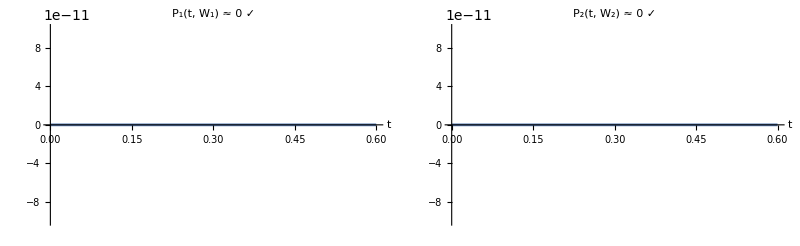
================= Equations: P₁(t, W₁) = 0 and P₂(t, W₂) = 0 =================
Let W₁ₛ₁ and W₁ₛ₂ be formulas for W₁(t) from solutions 1 and 2, respectively. Similarly, let W₂ₛ₁ and W₂ₛ₂ be the formulas for W₂(t). We show that all four pairs - (W₁ₛ₁, W₂ₛ₁), (W₁ₛ₁, W₂ₛ₂), (W₁ₛ₂, W₂ₛ₁), and (W₁ₛ₂, W₂ₛ₂) - solve equations P₁(t, W₁) = 0 and P₂(t, W₂) = 0.

Pair 1, (W₁, W₂) = (W₁ₛ₁, W₂ₛ₁):

P₁(t, W₁) = 1/((1. t^2+0.354727)^2)(t (t (1.9004×10^-16 t^4-1.52032×10^-15 t^2+3.88578×10^-16 √(-2.70096 t^4+2.67641 t^2+1) t-8.55179×10^-16)+7.63278×10^-17 √(-2.70096 t^4+2.67641 t^2+1))-1.12836×10^-16)

P₂(t, W₂) = 1/((1. t^2+0.331607)^2)(t (t (-1.0532×10^-16 t^4-5.6873×10^-16 t^2+7.63278×10^-17 √(-2.70096 t^4+2.67641 t^2+1) t-1.89577×10^-16)-2.08167×10^-17 √(-2.70096 t^4+2.67641 t^2+1))-1.0532×10^-17)

-Graphics-
Pair 2, (W₁, W₂) = (W₁ₛ₁, W₂ₛ₂):

P₁(t, W₁) = 1/((1. t^2+0.354727)^2)(t (t (1.9004×10^-16 t^4-1.52032×10^-15 t^2+3.88578×10^-16 √(-2.70096 t^4+2.67641 t^2+1) t-8.55179×10^-16)+7.63278×10^-17 √(-2.70096 t^4+2.67641 t^2+1))-1.12836×10^-16)

P₂(t, W₂) = 1/((1. t^2+0.331607)^2)(t (t (-1.0532×10^-16 t^4-5.6873×10^-16 t^2-7.63278×10^-17 √(-2.70096 t^4+2.67641 t^2+1) t-1.89577×10^-16)+2.08167×10^-17 √(-2.70096 t^4+2.67641 t^2+1))-1.0532×10^-17)

-Graphics-
Pair 3, (W₁, W₂) = (W₁ₛ₂, W₂ₛ₁):

P₁(t, W₁) = 1/((1. t^2+0.354727)^2)(t (t (1.9004×10^-16 t^4-1.52032×10^-15 t^2-3.88578×10^-16 √(-2.70096 t^4+2.67641 t^2+1) t-8.55179×10^-16)-7.63278×10^-17 √(-2.70096 t^4+2.67641 t^2+1))-1.12836×10^-16)

P₂(t, W₂) = 1/((1. t^2+0.331607)^2)(t (t (-1.0532×10^-16 t^4-5.6873×10^-16 t^2+7.63278×10^-17 √(-2.70096 t^4+2.67641 t^2+1) t-1.89577×10^-16)-2.08167×10^-17 √(-2.70096 t^4+2.67641 t^2+1))-1.0532×10^-17)

-Graphics-
Pair 4, (W₁, W₂) = (W₁ₛ₂, W₂ₛ₂):

P₁(t, W₁) = 1/((1. t^2+0.354727)^2)(t (t (1.9004×10^-16 t^4-1.52032×10^-15 t^2-3.88578×10^-16 √(-2.70096 t^4+2.67641 t^2+1) t-8.55179×10^-16)-7.63278×10^-17 √(-2.70096 t^4+2.67641 t^2+1))-1.12836×10^-16)

P₂(t, W₂) = 1/((1. t^2+0.331607)^2)(t (t (-1.0532×10^-16 t^4-5.6873×10^-16 t^2-7.63278×10^-17 √(-2.70096 t^4+2.67641 t^2+1) t-1.89577×10^-16)+2.08167×10^-17 √(-2.70096 t^4+2.67641 t^2+1))-1.0532×10^-17)

-Graphics-

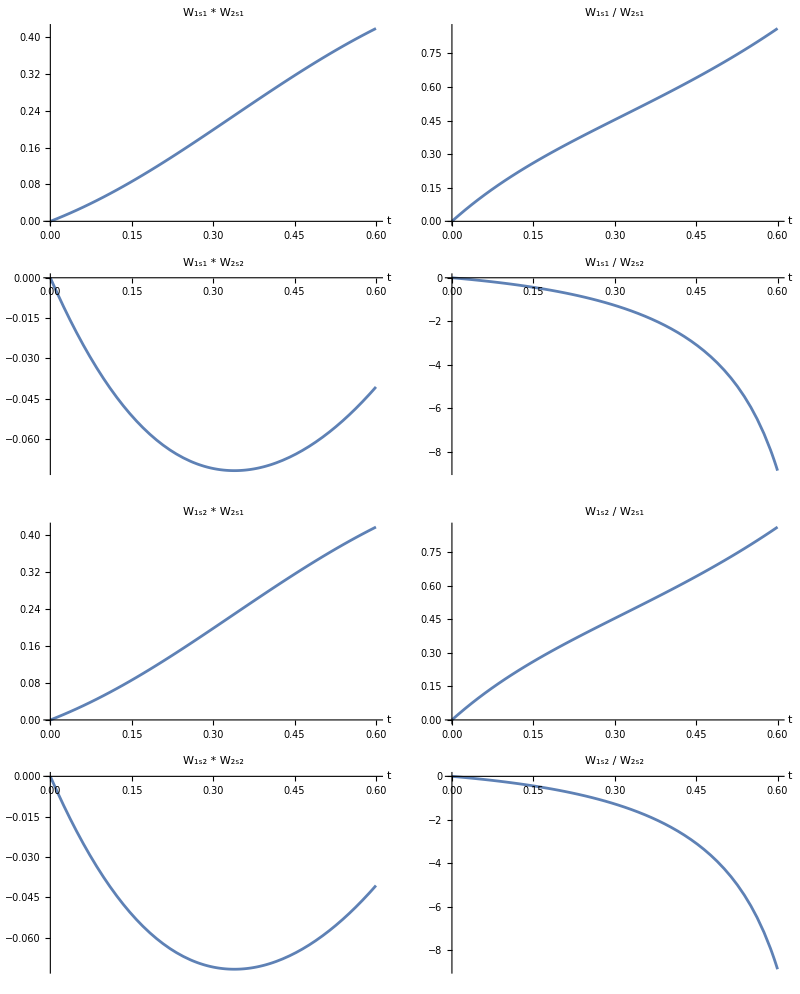
============= Plots of W₁(t)W₂(t) and W₁(t)/W₂(t) For All Pairs =============
Checking that all four pairs - (W₁ₛ₁, W₂ₛ₁), (W₁ₛ₁, W₂ₛ₂), (W₁ₛ₂, W₂ₛ₁), and (W₁ₛ₂, W₂ₛ₂) - does NOT satisfy W₁(t)/W₂(t) = const and W₁(t)W₂(t) = const.

-Graphics-

================= Equations: P₃(U, W₂) = 0 and P₄(U, W₁) = 0 =================
We solve P₃(U, W₂) = 0 and P₄(U, W₁) = 0 for W₁ and W₂.

W₁₁(U) = (7222744828955253 (189138201 U-(√(-2680395016262704482813187584807951930130653355908 U^4+1032129652347521584235818417642670330076442518838 U^2+149859397973825934530621273428105010794541324409))/(√28269114644460405884735498739639)))/(69343357 (34669481662129708 U^2+8063919601387767))
W₁₂(U) = (7222744828955253 ((√(-2680395016262704482813187584807951930130653355908 U^4+1032129652347521584235818417642670330076442518838 U^2+149859397973825934530621273428105010794541324409))/(√28269114644460405884735498739639)+189138201 U))/(69343357 (34669481662129708 U^2+8063919601387767))

W₂₁(U) = (36638176136907085 (639108280 U-(√(-171221835383724213721103870127558397470100713982038 U^4+65931749744600854023059486355485079809530328664611 U^2+9572917803121176424002017537029258858477782207750))/(√185529021411073059243794579716667)))/(158098757 (323189016543928223 U^2+86277416030895750))
W₂₂(U) = (36638176136907085 ((√(-171221835383724213721103870127558397470100713982038 U^4+65931749744600854023059486355485079809530328664611 U^2+9572917803121176424002017537029258858477782207750))/(√185529021411073059243794579716667)+639108280 U))/(158098757 (323189016543928223 U^2+86277416030895750))

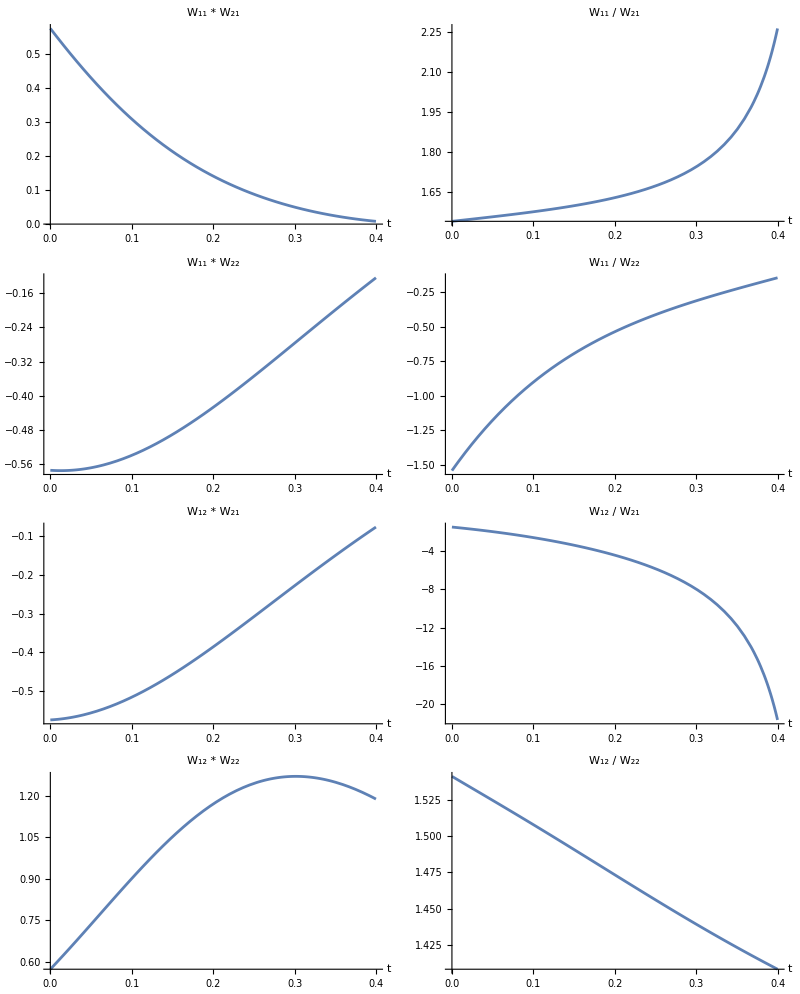
============= Plots of W₁(U)W₂(U) and W₁(U)/W₂(U) For All Pairs =============
Checking that all four pairs - (W₁₁(U), W₂₁(U)), (W₁₁(U), W₂₂(U)), (W₁₂(U), W₂₁(U)), and (W₁₂(U), W₂₂(U)) - does NOT satisfy W₁(U)/W₂(U) = const and W₁(U)W₂(U) = const.

-Graphics-

================= FLEXIBILITY (Double Checking) =================

Solution 1:

P_1(Z, W₁) = 1/((0.354727+1. t^2)^2)(-1.12836×10^-16+t (7.63278×10^-17 √(1+2.67641 t^2-2.70096 t^4)+t (-8.55179×10^-16-1.52032×10^-15 t^2+1.9004×10^-16 t^4+3.88578×10^-16 t √(1+2.67641 t^2-2.70096 t^4))))

P_2(Z, W₂) = 1/((0.331607+1. t^2)^2)(-1.0532×10^-17+t (-2.08167×10^-17 √(1+2.67641 t^2-2.70096 t^4)+t (-1.89577×10^-16-5.6873×10^-16 t^2-1.0532×10^-16 t^4+7.63278×10^-17 t √(1+2.67641 t^2-2.70096 t^4))))

P_3(U, W₂) = 1/((0.225014+1.01016 t^2+1. t^4)^2)(8.02692×10^-17+t (9.7296×10^-17 √(1+2.67641 t^2-2.70096 t^4)+t (6.42255×10^-16+t (4.21616×10^-16 √(1+2.67641 t^2-2.70096 t^4)+t (1.82917×10^-15+1.66701×10^-15 t^2+2.20538×10^-16 t^4+4.54048×10^-16 t √(1+2.67641 t^2-2.70096 t^4))))))

P_4(U, W₁) = 1/((0.240702+1.03328 t^2+1. t^4)^2)(2.31221×10^-16+t (4.95008×10^-16 √(1+2.67641 t^2-2.70096 t^4)+t (1.00956×10^-15+t (1.30265×10^-15 √(1+2.67641 t^2-2.70096 t^4)+t (9.90016×10^-16-1.0812×10^-15 t^2-2.60531×10^-16 t^4+4.81982×10^-16 t √(1+2.67641 t^2-2.70096 t^4))))))

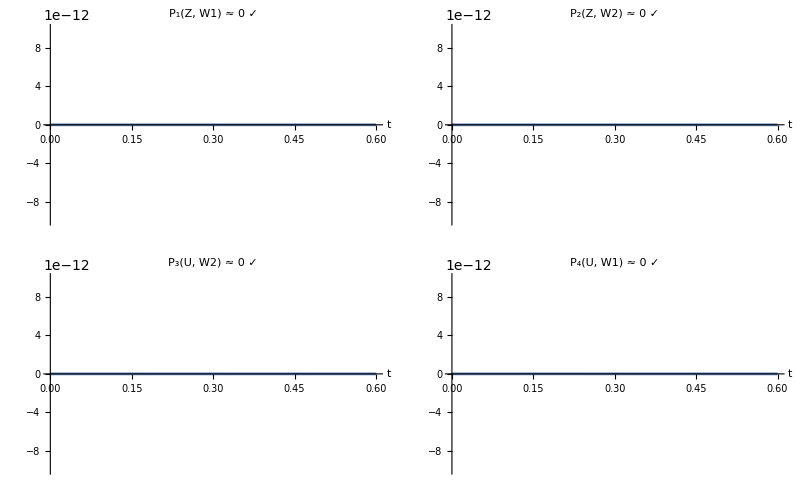
================= FLEXION 1 =================
Polynomials Pᵢ(t) built from Bricard’s equations for flexion 1.

-Graphics-

Solution 2:

P_1(Z, W₁) = 1/((0.354727+1. t^2)^2)(-1.12836×10^-16+t (-7.63278×10^-17 √(1+2.67641 t^2-2.70096 t^4)+t (-8.55179×10^-16-1.52032×10^-15 t^2+1.9004×10^-16 t^4-3.88578×10^-16 t √(1+2.67641 t^2-2.70096 t^4))))

P_2(Z, W₂) = 1/((0.331607+1. t^2)^2)(-1.0532×10^-17+t (2.08167×10^-17 √(1+2.67641 t^2-2.70096 t^4)+t (-1.89577×10^-16-5.6873×10^-16 t^2-1.0532×10^-16 t^4-7.63278×10^-17 t √(1+2.67641 t^2-2.70096 t^4))))

P_3(U, W₂) = 1/((0.225014+1.01016 t^2+1. t^4)^2)(8.02692×10^-17+t (-9.7296×10^-17 √(1+2.67641 t^2-2.70096 t^4)+t (6.42255×10^-16+t (-4.21616×10^-16 √(1+2.67641 t^2-2.70096 t^4)+t (1.82917×10^-15+1.66701×10^-15 t^2+2.20538×10^-16 t^4-4.54048×10^-16 t √(1+2.67641 t^2-2.70096 t^4))))))

P_4(U, W₁) = 1/((0.240702+1.03328 t^2+1. t^4)^2)(2.31221×10^-16+t (-4.95008×10^-16 √(1+2.67641 t^2-2.70096 t^4)+t (1.00956×10^-15+t (-1.30265×10^-15 √(1+2.67641 t^2-2.70096 t^4)+t (9.90016×10^-16-1.0812×10^-15 t^2-2.60531×10^-16 t^4-4.81982×10^-16 t √(1+2.67641 t^2-2.70096 t^4))))))

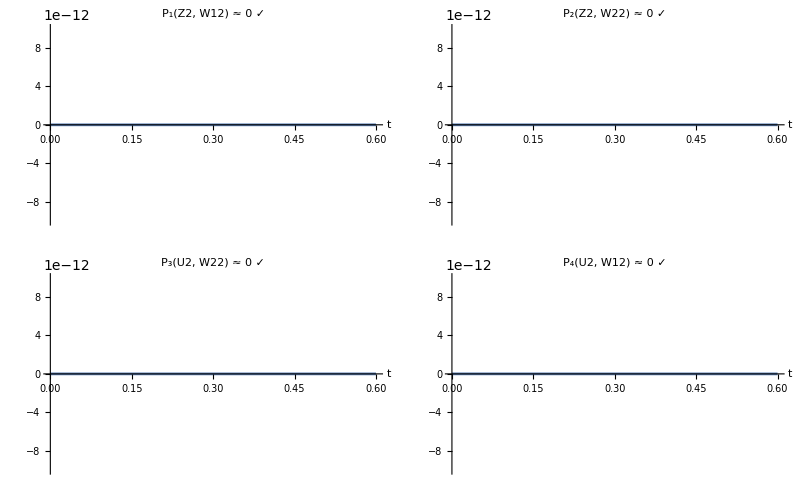
================= FLEXION 2 =================
Polynomials Pᵢ(t) built from Bricard’s equations for flexion 2.

-Graphics-

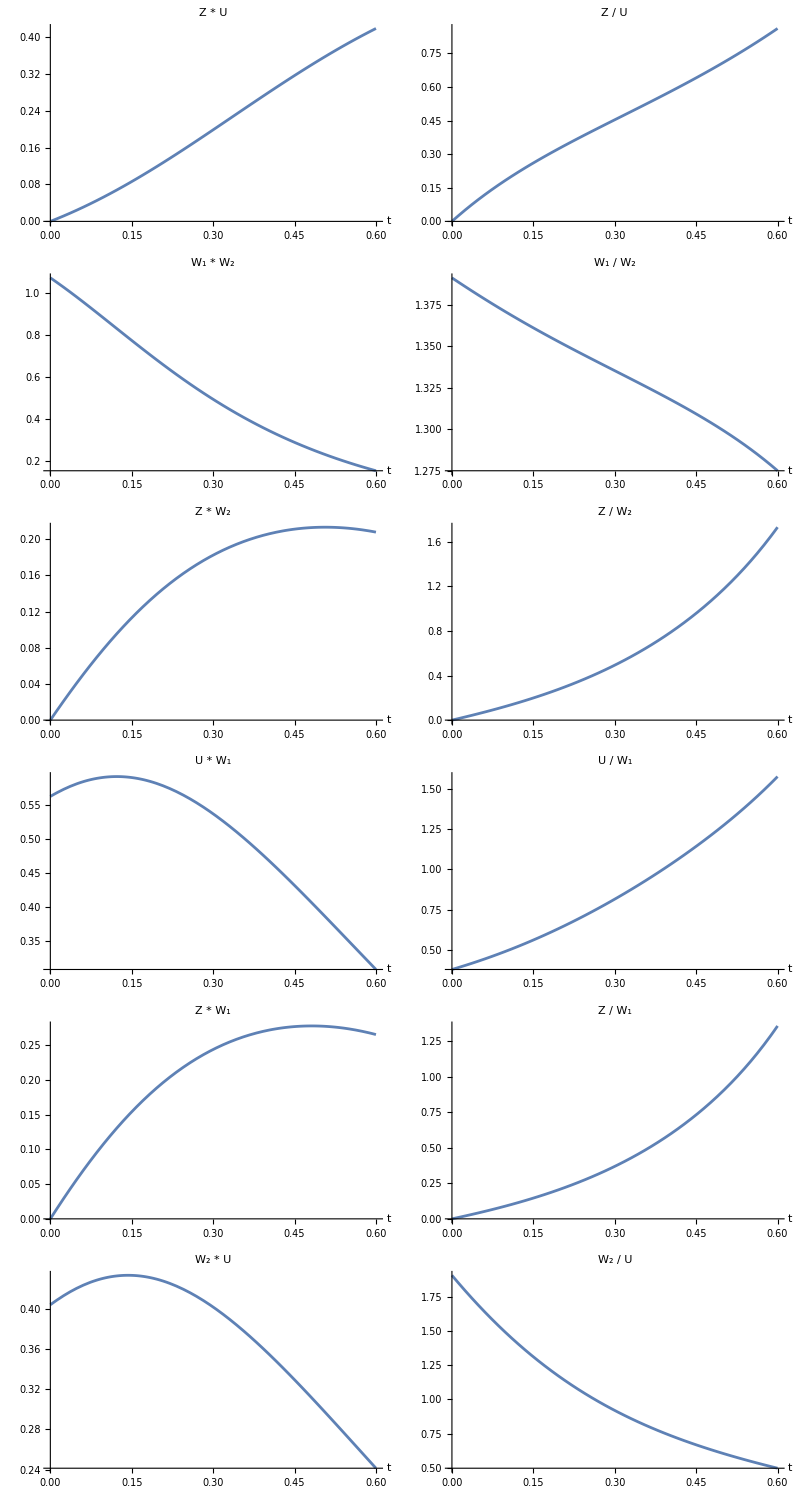
============= NOT LINEAR COMPOUND =============
Above we consider the first pair of equations (P₁(t, W₁) = 0 and P₂(t, W₂) = 0). Solving them as quadratic equations in W₁ and W₂, respectively we parametrize the solutions by the first two  and fourth expressions in Solutions 1 and 2 in a neighborhood of any point (W₁, t, W₂) such that the expression in the square root and denominators are not zero. Here, we choose any continuous branch of the square root in this neighborhood, and the signs in ± need Not agree (this means we consider all 4 pairs we describe above). We conclude that NO component of the solution set of the first pair of Bricard's equations satisfies W₁/W₂=const NOR W₁W₂=const.

Analogously, NO component of the solution set of the other pair of equations (P₃(U, W₂) = 0 and P₄(U, W₁) = 0) satisfies W₁/W₂=const NOR W₁W₂=const. As a result, NO component of the solution set of all four equations satisfies W₁/W₂=const NOR W₁W₂=const. So, our example does not belong to the linear compound class, even after switching the
boundary strips.

Below, we also present the plots of functions ZU, Z/U, W₁W₂, W₁/W₂, ZW₂, Z/W₂, UW₁, U/W₁, ZW₁, Z/W₁, W₂U, W₂/U.

Solution 1:

-Graphics-

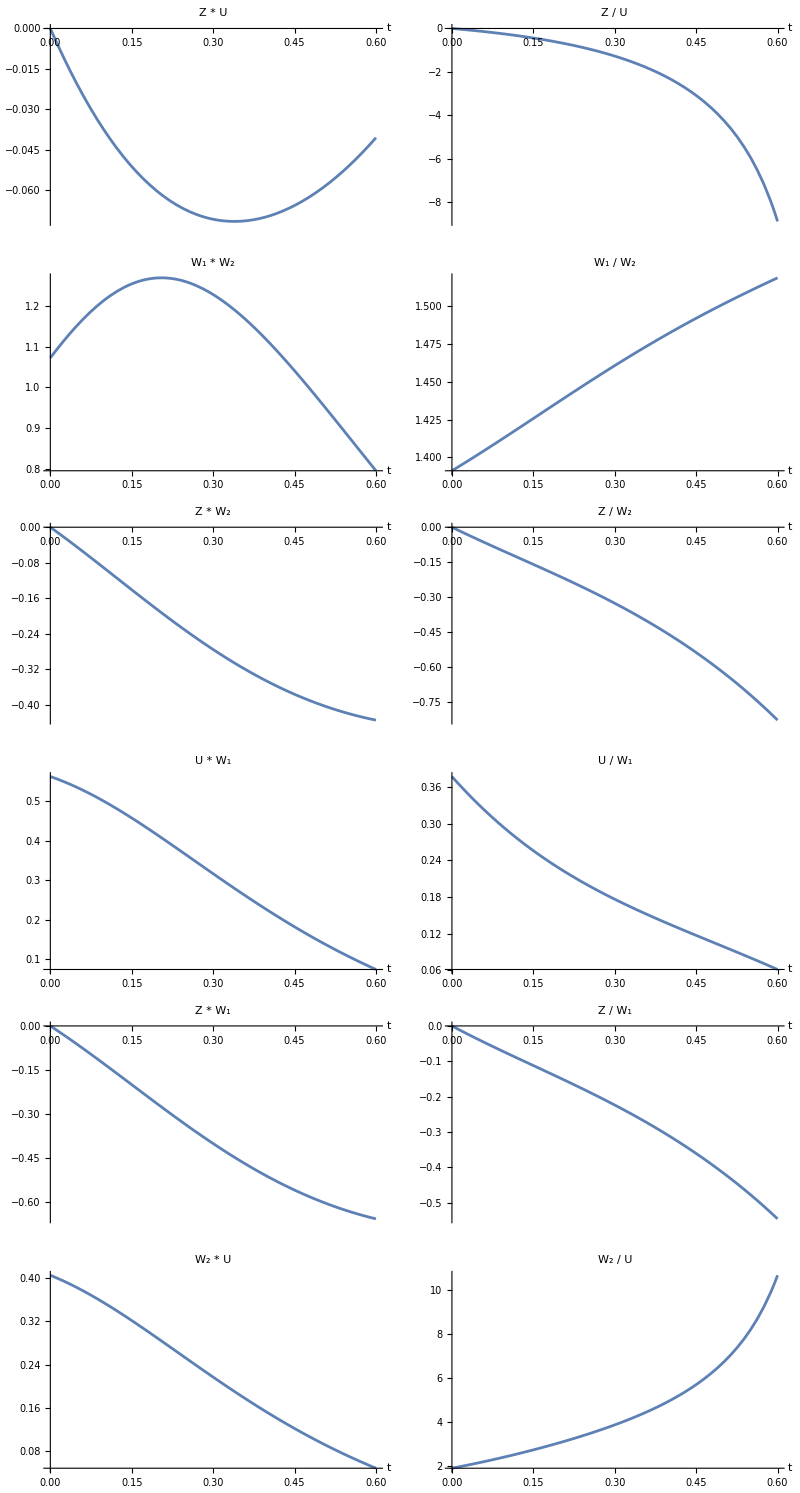
Solution 2:

-Graphics-

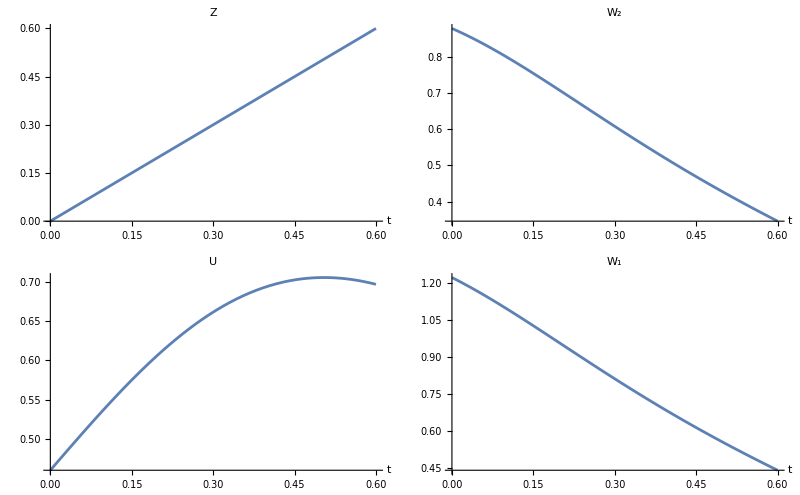
================= NOT TRIVIAL (FLEXION 1) =================
This configuration does not belong to the trivial class — even after switching the boundary strips — since none of the functions Z, W2, U, or W1 is constant.

-Graphics-

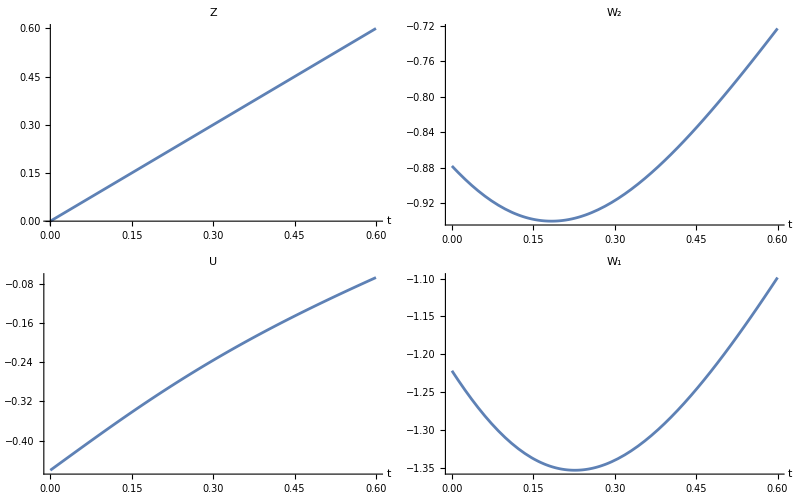
================= NOT TRIVIAL (FLEXION 2) =================
This configuration does not belong to the trivial class — even after switching the boundary strips — since none of the functions Z, W2, U, or W1 is constant.

-Graphics-

================= NOT CONIC & NOT CHIMERA & NOT LINEAR CONJUGATE & NOT ISOGONAL=================
Condition (N.0) is satisfied for all i=1,...,4 ⇒ NOT equimodular-conic, NOT chimera, NOT isogonal and NOT linear conjugate. Applying any boundary-strip switch still preserves (N.0), so no conic, no chimera, no isogonal and no linear conjugate form emerges.

CONDITION (N.0) AFTER SWITCHING BOUNDARY STRIPS
Right: Condition (N.0) is still satisfied.
Left: Condition (N.0) is still satisfied.
Lower: Condition (N.0) is still satisfied.
Upper: Condition (N.0) is still satisfied.
Right + Left: Condition (N.0) is still satisfied.
Right + Lower: Condition (N.0) is still satisfied.
Right + Upper: Condition (N.0) is still satisfied.
Left + Lower: Condition (N.0) is still satisfied.
Left + Upper: Condition (N.0) is still satisfied.
Lower + Upper: Condition (N.0) is still satisfied.
Right + Left + Lower: Condition (N.0) is still satisfied.
Right + Left + Upper: Condition (N.0) is still satisfied.
Right + Lower + Upper: Condition (N.0) is still satisfied.
Left + Lower + Upper: Condition (N.0) is still satisfied.
Right + Left + Lower + Upper: Condition (N.0) is still satisfied.

================= ORTHOGONALITY CHECK =================
cos(αᵢ)·cos(γᵢ) ≠ cos(βᵢ)·cos(δᵢ) for at least one i = 1,..., 4 ⇒ NOT orthodiagonal. Switching boundary strips does not correct this.

Initial anglesDeg (no switches):

-> Condition met: At least one difference is non-zero.

NON-ORTHOGONALITY CHECK AFTER SWITCHING BOUNDARY STRIPS
Right: Condition met (at least one difference is non-zero).
Left: Condition met (at least one difference is non-zero).
Lower: Condition met (at least one difference is non-zero).
Upper: Condition met (at least one difference is non-zero).
Right + Left: Condition met (at least one difference is non-zero).
Right + Lower: Condition met (at least one difference is non-zero).
Right + Upper: Condition met (at least one difference is non-zero).
Left + Lower: Condition met (at least one difference is non-zero).
Left + Upper: Condition met (at least one difference is non-zero).
Lower + Upper: Condition met (at least one difference is non-zero).
Right + Left + Lower: Condition met (at least one difference is non-zero).
Right + Left + Upper: Condition met (at least one difference is non-zero).
Right + Lower + Upper: Condition met (at least one difference is non-zero).
Left + Lower + Upper: Condition met (at least one difference is non-zero).
Right + Left + Lower + Upper: Condition met (at least one difference is non-zero).

================= CONJUGATE-MODULAR CHECK =================
M1 = M2 = M3 = M4 = M and M ≠ 2 ⇒ NOT conjugate-modular. Boundary-strip switches preserve this.

Initial anglesDeg (no switches):

-> Condition met: All Mᵢ are equal and M ≠ 2.

CONJUGATE-MODULAR CHECK AFTER SWITCHING BOUNDARY STRIPS
Right: Condition met (All Mᵢ are equal and M ≠ 2).
Left: Condition met (All Mᵢ are equal and M ≠ 2).
Lower: Condition met (All Mᵢ are equal and M ≠ 2).
Upper: Condition met (All Mᵢ are equal and M ≠ 2).
Right + Left: Condition met (All Mᵢ are equal and M ≠ 2).
Right + Lower: Condition met (All Mᵢ are equal and M ≠ 2).
Right + Upper: Condition met (All Mᵢ are equal and M ≠ 2).
Left + Lower: Condition met (All Mᵢ are equal and M ≠ 2).
Left + Upper: Condition met (All Mᵢ are equal and M ≠ 2).
Lower + Upper: Condition met (All Mᵢ are equal and M ≠ 2).
Right + Left + Lower: Condition met (All Mᵢ are equal and M ≠ 2).
Right + Left + Upper: Condition met (All Mᵢ are equal and M ≠ 2).
Right + Lower + Upper: Condition met (All Mᵢ are equal and M ≠ 2).
Left + Lower + Upper: Condition met (All Mᵢ are equal and M ≠ 2).
Right + Left + Lower + Upper: Condition met (All Mᵢ are equal and M ≠ 2).

```mathematica
(*================================================================================*)
(*================================================================================*)
(*================================================================================*)
(*Quit*)
(*All angle sets in degrees*)
anglesDeg={
{26.20863403213998,82.2407675648952,21.949109994264898,60},(*Vertex 1*)
{16.166237389600262,130.87095233025335,18.85247535405415,115},(*Vertex 2*)
{134.65533802039442,34.44439013740831,145.3694664686027,80},(*Vertex 3*)
{117.95117201340666,49.52829397349284,149.0275482144225,105}  (*Vertex 4*)};


(*-------------------------------------------*)
(*Function to compute sigma from 4 angles*)
computeSigma[{α_,β_,γ_,δ_}]:=(α+β+γ+δ)/2;

(*-------------------------------------------*)
(*Function to compute a,b,c,d from angles*)
computeABCD[{α_,β_,γ_,δ_}]:=Module[{alpha=α Degree,beta=β Degree,gamma=γ Degree,delta=δ Degree,sigma},sigma=computeSigma[{α,β,γ,δ} Degree];
{Sin[alpha]/Sin[sigma-alpha],Sin[beta]/Sin[sigma-beta],Sin[gamma]/Sin[sigma-gamma],Sin[delta]/Sin[sigma-delta]}];

(*-------------------------------------------*)
(*Compute all σ values*)
sigmas=computeSigma/@anglesDeg;

(*Compute all {a,b,c,d} values*)
results=computeABCD/@anglesDeg;

(*Optional:extract individual values*)
{a1,b1,c1,d1}=results[[1]];
{a2,b2,c2,d2}=results[[2]];
{a3,b3,c3,d3}=results[[3]];
{a4,b4,c4,d4}=results[[4]];
{σ1,σ2,σ3,σ4}=FullSimplify[sigmas];


(*================================================================================*)
(*================================CONDITION (N.0)=================================*)
(*================================================================================*)
(*uniqueCombos={{1,1,1,1},{1,1,1,-1},{1,1,-1,-1},{1,1,-1,1},{1,-1,1,1},{1,-1,-1,1},{1,-1,1,-1},{1,-1,-1,-1}};

checkConditionN0Degrees[{α_,β_,γ_,δ_}]:=Module[{angles={α,β,γ,δ},results},results=Mod[uniqueCombos.angles,360]//Chop;
!MemberQ[results,0]];

conditionsN0=checkConditionN0Degrees/@anglesDeg;
allVerticesPass=And@@conditionsN0;

Column[{TextCell[Style["================= CONDITION (N.0) =================",Darker[Green],Bold, 16],"Text"],
If[allVerticesPass,
Style["✔ All vertices satisfy (N.0).",Darker[Green],Bold],Style["✘ Some vertices fail (N.0).",Red,Bold]]}]*)
uniqueCombos={{1,1,1,1},{1,1,1,-1},{1,1,-1,-1},{1,1,-1,1},{1,-1,1,1},{1,-1,-1,1},{1,-1,1,-1},{1,-1,-1,-1}};

checkConditionN0Degrees[{α_,β_,γ_,δ_}]:=Module[{angles={α,β,γ,δ},results},results=Mod[uniqueCombos.angles,360]//Chop;
results];

(*apply to all vertices*)
resultsPerVertex=checkConditionN0Degrees/@anglesDeg;

(*check pass/fail*)
conditionsN0=Map[!MemberQ[#,0]&,resultsPerVertex];
allVerticesPass=And@@conditionsN0;

Column[{TextCell[Style["================= CONDITION (N.0) =================",Darker[Green],Bold,16],"Text"],(*summary line*)If[allVerticesPass,Style["✔ All vertices satisfy (N.0).",Darker[Green],Bold],Style["✘ Some vertices fail (N.0).",Red,Bold]],(*detailed results for each vertex*)Grid[Prepend[Table[{"Vertex "<>ToString[i],resultsPerVertex[[i]],If[conditionsN0[[i]],"✔ Pass","✘ Fail"]},{i,Length[anglesDeg]}],{"Vertex","Combinations (mod 360)","Status"}],Frame->All]}]


(*================================================================================*)
(*================================CONDITION (N.3)=================================*)
(*================================================================================*)
Ms=FullSimplify[Times@@@results];
allEqualQ=Simplify[Equal@@Ms];

Column[{TextCell[Style["================= CONDITION (N.3) =================",Darker[Blue],Bold, 16],"Text"],If[allEqualQ,
Row[{Style["✔ M1 = M2 = M3 = M4 = ",Bold],Ms[[1]]}],Style["✘ M_i are not all equal.",Red,Bold]]}]


(*================================================================================*)
(*===========================CONDITION (N.4)===========================*)
(*================================================================================*)
aList=results[[All,1]];
cList=results[[All,3]];
dList=results[[All,4]];

rList=FullSimplify/@(aList*dList);{r1,r2,r3,r4}=rList;
sList=FullSimplify/@(cList*dList);{s1,s2,s3,s4}=sList;

Column[{TextCell[Style["================= CONDITION (N.4) =================",Darker[Purple],Bold, 16],"Text"],If[r1==r2&&r3==r4&&s1==s4&&s2==s3,Column[{Row[{Style["✔ r1 = r2 = ",Bold],r1, Style["; ✔ r3 = r4 = ",Bold],r3}],Row[{Style["✔ s1 = s4 = ",Bold],s1, Style["; ✔ s2 = s3 = ",Bold],s2}]}],Style["✘ Condition (N.4) fails.",Red,Bold]]
}]


(*================================================================================*)
(*=================================CONDITION (N.5)===============================*)
(*================================================================================*)
fList=FullSimplify/@(aList*cList);{f1,f2,f3,f4}=fList;
M1=Ms[[1]];

m[M1_]:=Piecewise[{{1-M1,M1<1},{(M1-1)/M1,M1>1}}]//N;
K=EllipticK[m[M1]]//N;
Kp=EllipticK[1-m[M1]]//N;

computeTi[i_]:=Module[{sigma=sigmas[[i]],r=rList[[i]],s=sList[[i]],f=fList[[i]],base},base=I*Im[InverseJacobiDN[Piecewise[{{Sqrt[f],M1<1},{1/Sqrt[f],M1>1}}],m[M1]]] / Kp;
Which[sigma<180,Which[r>1&&s>1,base,(r<1&&s>1)||(r>1&&s<1),1+base,r<1&&s<1,2+base],sigma>180,Which[r>1&&s>1,2+base,(r<1&&s>1)||(r>1&&s<1),3+base,r<1&&s<1,base]]];

tList=computeTi/@Range[4];
RoundWithTolerance[x_,tol_:10^(-14)]:=Module[{nearest},nearest=Round[x];
If[Abs[x-nearest]<=tol,nearest,x]];

checkValidCombination[M1_,ε_:10^(-14)]:=Module[{i,combo,dotProd,rePart,imPart,n2,expr,foundQ=False},Print[Style["⚠ Approximate validation using ε-tolerance. For rigorous proof, see the referenced paper.",Darker@Orange,Italic]];
Do[combo=uniqueCombos[[i]];
dotProd=tList.combo;
rePart=Abs[Re[dotProd]];
imPart=Abs[Im[dotProd]];
If[M1<1,
If[Mod[RoundWithTolerance[rePart], 4]<ε,
If[Mod[RoundWithTolerance[imPart], 2]<ε,expr=tList[[1]]+combo[[2]] tList[[2]]+combo[[3]] tList[[3]]+combo[[4]] tList[[4]];
Print[Style["✅ Valid Combination Found (M < 1):",Darker[Green],Bold],"\n",Style["e1 = ", Bold],combo[[2]],Style[", e2 = ", Bold],combo[[3]],Style[", e3 = ", Bold],combo[[4]],"\n",Style["t1 = ", Bold],Re[tList[[1]]],"K + ",Im[tList[[1]]],"iK'","\n",Style["t2 = ", Bold],Re[tList[[2]]],"K + ",Im[tList[[2]]],"iK'","\n",Style["t3 = ", Bold],Re[tList[[3]]],"K + ",Im[tList[[3]]],"iK'","\n",Style["t4 = ", Bold],Re[tList[[4]]],"K + ",Im[tList[[4]]],"iK'","\n",Style["t1 + e1*t2 + e2*t3 + e3*t4 = ", Bold],Re[expr],"K + ",Im[expr],"iK'"];
foundQ=True;
Break[]]]];
If[M1>1,
If[Mod[RoundWithTolerance[imPart], 2]<ε, n2=Quotient[RoundWithTolerance[imPart], 2];
If[Mod[RoundWithTolerance[Abs[rePart-2 n2]], 4]<ε,expr=tList[[1]]+combo[[2]] tList[[2]]+combo[[3]] tList[[3]]+combo[[4]] tList[[4]];
Print[Style["✅ Valid Combination Found (M > 1):",Darker[Green],Bold],"\n",Style["e1 = ", Bold],combo[[2]],Style[", e2 = ", Bold],combo[[3]],Style[", e3 = ", Bold],combo[[4]],"\n",Style["t1 = ", Bold],Re[tList[[1]]],"K + ",Im[tList[[1]]],"iK'","\n",Style["t2 = ", Bold],Re[tList[[2]]],"K + ",Im[tList[[2]]],"iK'","\n",Style["t3 = ", Bold],Re[tList[[3]]],"K + ",Im[tList[[3]]],"iK'","\n",Style["t4 = ", Bold],Re[tList[[4]]],"K + ",Im[tList[[4]]],"iK'","\n",Style["t1 + e1*t2 + e2*t3 + e3*t4 = ", Bold],Re[expr],"K + ",Im[expr],"iK'"];
foundQ=True;
Break[]]]],{i,Length[uniqueCombos]}];
If[!foundQ,Print[Style["❌ No valid combination found.",Red,Bold],"\n",Style["t1 = ", Bold],Re[tList[[1]]],"K + ",Im[tList[[1]]],"iK'","\n",Style["t2 = ", Bold],Re[tList[[2]]],"K + ",Im[tList[[2]]],"iK'","\n",Style["t3 = ", Bold],Re[tList[[3]]],"K + ",Im[tList[[3]]],"iK'","\n",Style["t4 = ", Bold],Re[tList[[4]]],"K + ",Im[tList[[4]]],"iK'","\n"]];];


Column[{TextCell[Style["================= CONDITION (N.5) =================",Darker[Red],Bold, 16],"Text"]}]
res=checkValidCombination[M1];


(*================================================================================*)
(*================================OTHER PARAMETER=================================*)
(*================================================================================*)
cosSigmaAlt[Mi_,fi_,ri_,si_]:=(Mi (fi+ri+si-1)+ri fi si-ri fi-ri si-fi si)/(2 Sqrt[ri si fi] (1-Mi));

Column[
{TextCell[Style["================= OTHER PARAMETERS =================",Darker[Orange],Bold,16],"Text"],
Row[{Style["u = ", Bold], 1 - M1}], Row[{Style["σ1 = ", Bold],σ1 Degree,Style[", σ2 = ", Bold],σ2 Degree,Style[", σ3 = ", Bold],σ3 Degree,Style[", σ4 = ", Bold],σ4 Degree}],
Row[{Style["σ1 ≈ ", Bold],N[σ1], Style["°", Bold],Style[", σ2 ≈ ", Bold],N[σ2],Style["°", Bold],Style[", σ3 ≈ ", Bold],N[σ3],Style["°", Bold],Style[", σ4 ≈ ", Bold],N[σ4],Style["°", Bold]}],
Row[{Style["cosσ1 = ",Bold],Simplify@cosSigmaAlt[M1,f1,r1,s1],Style[", cosσ2 = ",Bold],Simplify@cosSigmaAlt[M1,f2,r2,s2],Style[", cosσ3 = ",Bold],Simplify@cosSigmaAlt[M1,f3,r3,s3],Style[", cosσ4 = ",Bold],Simplify@cosSigmaAlt[M1,f4,r4,s4]}],
Row[{Style["f1 = ", Bold],f1,Style[", f2 = ", Bold],f2,Style[", f3 = ", Bold],f3,Style[", f4 = ", Bold],f4}],Row[{Style["z1 = ", Bold],FullSimplify[1/(f1-1)],Style[", z2 = ", Bold],FullSimplify[1/(f2-1)],Style[", z3 = ", Bold],FullSimplify[1/(f3-1)],Style[", z4 = ", Bold],FullSimplify[1/(f4-1)]}],Row[{Style["x1 = ", Bold],FullSimplify[1/(r1-1)],Style[", x2 = ", Bold],FullSimplify[1/(r2-1)],Style[", x3 = ", Bold],FullSimplify[1/(r3-1)],Style[", x4 = ", Bold],FullSimplify[1/(r4-1)]}],Row[{Style["y1 = ", Bold],FullSimplify[1/(s1-1)],Style[", y2 = ", Bold],FullSimplify[1/(s2-1)],Style[", y3 = ", Bold],FullSimplify[1/(s3-1)],Style[", y4 = ", Bold],FullSimplify[1/(s4-1)]}],
Row[{Style["p1 = ", Bold],Simplify[Sqrt[r1-1]],Style[", p2 = ", Bold],Simplify[Sqrt[r2-1]],Style[", p3 = ", Bold],Simplify[Sqrt[r3-1]],Style[", p4 = ", Bold],Simplify[Sqrt[r4-1]]}],
Row[{Style["q1 = ", Bold],Simplify[Sqrt[s1-1]],Style[", q2 = ", Bold],Simplify[Sqrt[s2-1]],Style[", q3 = ", Bold],Simplify[Sqrt[s3-1]],Style[", q4 = ", Bold],Simplify[Sqrt[s4-1]]}],
Row[{Style["p1·q1 = ", Bold],Simplify[Sqrt[r1-1] Sqrt[s1-1]],Style[", p2·q2 = ", Bold],Simplify[Sqrt[r2-1] Sqrt[s2-1]],Style[", p3·q3 = ", Bold],Simplify[Sqrt[r3-1] Sqrt[s3-1]],Style[", p4·q4 = ", Bold],Simplify[Sqrt[r4-1] Sqrt[s4-1]]}]
}]


(*================================================================================*)
(*==============================BRICARD's EQUATIONS==============================*)
(*================================================================================*)
(*Bricard's equation as defined in terms of angles and variables*)
BricardsEquation[{α_,β_,γ_,δ_},σ_,x_,y_]:=Module[
{c22,c20,c02,c11,c00},
c22=Sin[σ-δ] Sin[σ-δ-β];
c20=Sin[σ-α] Sin[σ-α-β];
c02=Sin[σ-γ] Sin[σ-γ-β];
c11=-Sin[α] Sin[γ];
c00=Sin[σ] Sin[σ-β];
c22 x^2 y^2+c20 x^2+c02 y^2+2 c11 x y+c00
];

(*Step 1: Bricard's system of equations*)
Column[{(*Header*)TextCell[Style["================= Bricard's System of Equations =================",Darker[Purple],Bold,16],"Text"],(*Explanatory note*)
Row[{TextCell[Style["We introduce new notation for the cotangents of half of the dihedral angles. Denote Z:= ",GrayLevel[0.3],13],"Text"],TraditionalForm[cot[Subscript[θ,1]/2]],TextCell[Style[", W₂= ",GrayLevel[0.3],13],"Text"],TraditionalForm[cot[Subscript[θ,2]/2]], TextCell[Style[", U:= ",GrayLevel[0.3],13],"Text"],TraditionalForm[cot[Subscript[θ,3]/2]],
TextCell[Style[", and W₁= ",GrayLevel[0.3],13],"Text"],TraditionalForm[cot[Subscript[θ,4]/2]]
}], Spacer[12],
(*Traditional form results*)Row[{"P₁(Z, W₁) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[1]] Degree,sigmas[[1]] Degree,Z,W₁]], W₁]], " = 0"}],Spacer[6],
Row[{"P₂(Z, W₂) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[2]] Degree,sigmas[[2]] Degree,Z,W₂]], W₂]], " = 0"}],Spacer[6],
Row[{"P₃(U, W₂) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[3]] Degree,sigmas[[3]] Degree,U,W₂]],W₂]], " = 0"}],Spacer[6],
Row[{"P₄(U, W₁) = ",TraditionalForm[Collect[FullSimplify[BricardsEquation[anglesDeg[[4]] Degree,sigmas[[4]] Degree,U,W₁]],W₁]], " = 0"}]
}]
(*==================================FLEXION 1==================================*)

Z[t_] :=t;
W1[t_]:=(1.8303883744906646 (0.739190870110122 t-0.8185802872931142 √((1+3.4575776313801847 t^2) (1-0.7811714739558353 t^2))))/(-1.2264950862699229-3.4575776313801847 t^2);
U[t_] :=(0.18029302872898165 (11.610011024543208 t+6.663793331850769 √((1+3.4575776313801847 t^2) (1-0.7811714739558353 t^2))))/(2.6091661366212175+3.845171738795376 t^2);
W2[t_] := (0.8842187622039149 (0.8494336559689466 t-1.1387226496890441 √((1+3.4575776313801847 t^2) (1-0.7811714739558353 t^2))))/(-1.1465569838598522-3.4575776313801847 t^2);

(*==================================FLEXION 2==================================*)
Z2[t_] :=t;
W12[t_]:=(1.8303883744906646 (0.739190870110122 t+0.8185802872931142 √((1+3.4575776313801847 t^2) (1-0.7811714739558353 t^2))))/(-1.2264950862699229-3.4575776313801847 t^2);
U2[t_] :=(0.18029302872898165 (11.610011024543208 t-6.663793331850769 √((1+3.4575776313801847 t^2) (1-0.7811714739558353 t^2))))/(2.6091661366212175+3.845171738795376 t^2);
W22[t_] := (0.8842187622039149 (0.8494336559689466 t+1.1387226496890441 √((1+3.4575776313801847 t^2) (1-0.7811714739558353 t^2))))/(-1.1465569838598522-3.4575776313801847 t^2);

(*Step 2: Formulas for flexions*)
Column[{(*Header*)TextCell[Style["================= FLEXIONS =================",Red,Bold,16],"Text"],(*Explanatory note*)TextCell[Style["Solutions to Bricard's equations under a free parameter t := Z ∈ ℂ:",GrayLevel[0.3],13],"Text"],Spacer[12],
(*Heading for results*)TextCell[Style["Solution 1:",Bold,14],"Text"],Spacer[6],(*Traditional form results*)Row[{"Z(t) = ",TraditionalForm[FullSimplify[Z[t]]]}],Spacer[6],
Row[{"W₂(t) = ",TraditionalForm[FullSimplify[W2[t]]]}],Spacer[6],
Row[{"U(t) = ",TraditionalForm[FullSimplify[U[t]]]}],Spacer[6],
Row[{"W₁(t) = ",TraditionalForm[FullSimplify[W1[t]]]}],  Spacer[12],
(*Heading for results*)TextCell[Style["Solution 2:",Bold,14],"Text"],Spacer[6],(*Traditional form results*)Row[{"Z(t) = ",TraditionalForm[FullSimplify[Z2[t]]]}],Spacer[6],
Row[{"W₂(t) = ",TraditionalForm[FullSimplify[W22[t]]]}],Spacer[6],
Row[{"U(t) = ",TraditionalForm[FullSimplify[U2[t]]]}],Spacer[6],
Row[{"W₁(t) = ",TraditionalForm[FullSimplify[W12[t]]]}]
}]

(*Step 3: Checking that W₁(t) and W₂(t) solves P₁(t, W₁) = 0 and P₂(t, W₂) = 0 even when +- signs do NOT agree*)
(*t-range*)
tMin=0;
tMax= 0.6;

Column[{(*Header*)TextCell[Style["================= Equations: P₁(t, W₁) = 0 and P₂(t, W₂) = 0 =================",Orange,Bold,16],"Text"],(*Explanatory note*)TextCell[Style["Let W₁ₛ₁ and W₁ₛ₂ be formulas for W₁(t) from solutions 1 and 2, respectively. Similarly, let W₂ₛ₁ and W₂ₛ₂ be the formulas for W₂(t). We show that all four pairs - (W₁ₛ₁, W₂ₛ₁), (W₁ₛ₁, W₂ₛ₂), (W₁ₛ₂, W₂ₛ₁), and (W₁ₛ₂, W₂ₛ₂) - solve equations P₁(t, W₁) = 0 and P₂(t, W₂) = 0.",GrayLevel[0.3],13],"Text"],Spacer[12],
(*Heading for results*)

TextCell[Style["Pair 1, (W₁, W₂) = (W₁ₛ₁, W₂ₛ₁):",Bold,14],"Text"],Spacer[6],(*Traditional form results*)Row[{"P₁(t, W₁) = ",TraditionalForm[FullSimplify[BricardsEquation[anglesDeg[[1]] Degree,sigmas[[1]] Degree,Z[t], W1[t]]]]}],Spacer[6],
Row[{"P₂(t, W₂) = ",TraditionalForm[FullSimplify[BricardsEquation[anglesDeg[[2]] Degree,sigmas[[2]] Degree,Z[t],W2[t]]]]}],Spacer[12],
(*Verification Plots Module:This entire Module is now the last item inside the main Column.It will execute and place the resulting Panel here.*)Module[{PiExpr,labels},(*1. Define the two polynomial expressions to be plotted*)PiExpr={FullSimplify[BricardsEquation[anglesDeg[[1]] Degree,sigmas[[1]] Degree,Z[t],W1[t]]],FullSimplify[BricardsEquation[anglesDeg[[2]] Degree,sigmas[[2]] Degree,Z[t],W2[t]]]};
(*2. Define the labels for each plot*)labels={Row[{Subscript["P",1],"(t, ",Subscript["W",1],")", " ≈ 0 ",Style["✓",Darker[Green],Bold]}],Row[{Subscript["P",2],"(t, ",Subscript["W",2],")", " ≈ 0 ",Style["✓",Darker[Green],Bold]}]};
(*3. Display the plots in the specified panel style*)Panel[GraphicsGrid[Partition[Table[Plot[PiExpr[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->{-10^-10,10^-10},(*Zoom in to confirm zero*)AxesLabel->{"t",None},ImageSize->300],{i,Length[PiExpr]}],2 (*Arrange plots in rows of 2*)],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]],

TextCell[Style["Pair 2, (W₁, W₂) = (W₁ₛ₁, W₂ₛ₂):",Bold,14],"Text"],Spacer[6],(*Traditional form results*)Row[{"P₁(t, W₁) = ",TraditionalForm[FullSimplify[BricardsEquation[anglesDeg[[1]] Degree,sigmas[[1]] Degree,Z[t], W1[t]]]]}],Spacer[6],
Row[{"P₂(t, W₂) = ",TraditionalForm[FullSimplify[BricardsEquation[anglesDeg[[2]] Degree,sigmas[[2]] Degree,Z[t],W22[t]]]]}],Spacer[12],
(*Verification Plots Module:This entire Module is now the last item inside the main Column.It will execute and place the resulting Panel here.*)Module[{PiExpr,labels},(*1. Define the two polynomial expressions to be plotted*)PiExpr={FullSimplify[BricardsEquation[anglesDeg[[1]] Degree,sigmas[[1]] Degree,Z[t],W1[t]]],FullSimplify[BricardsEquation[anglesDeg[[2]] Degree,sigmas[[2]] Degree,Z[t],W22[t]]]};
(*2. Define the labels for each plot*)labels={Row[{Subscript["P",1],"(t, ",Subscript["W",1],")", " ≈ 0 ",Style["✓",Darker[Green],Bold]}],Row[{Subscript["P",2],"(t, ",Subscript["W",2],")", " ≈ 0 ",Style["✓",Darker[Green],Bold]}]};
(*3. Display the plots in the specified panel style*)Panel[GraphicsGrid[Partition[Table[Plot[PiExpr[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->{-10^-10,10^-10},(*Zoom in to confirm zero*)AxesLabel->{"t",None},ImageSize->300],{i,Length[PiExpr]}],2 (*Arrange plots in rows of 2*)],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]],

TextCell[Style["Pair 3, (W₁, W₂) = (W₁ₛ₂, W₂ₛ₁):",Bold,14],"Text"],Spacer[6],(*Traditional form results*)Row[{"P₁(t, W₁) = ",TraditionalForm[FullSimplify[BricardsEquation[anglesDeg[[1]] Degree,sigmas[[1]] Degree,Z[t], W12[t]]]]}],Spacer[6],
Row[{"P₂(t, W₂) = ",TraditionalForm[FullSimplify[BricardsEquation[anglesDeg[[2]] Degree,sigmas[[2]] Degree,Z[t],W2[t]]]]}],Spacer[12],
(*Verification Plots Module:This entire Module is now the last item inside the main Column.It will execute and place the resulting Panel here.*)Module[{PiExpr,labels},(*1. Define the two polynomial expressions to be plotted*)PiExpr={FullSimplify[BricardsEquation[anglesDeg[[1]] Degree,sigmas[[1]] Degree,Z[t],W12[t]]],FullSimplify[BricardsEquation[anglesDeg[[2]] Degree,sigmas[[2]] Degree,Z[t],W2[t]]]};
(*2. Define the labels for each plot*)labels={Row[{Subscript["P",1],"(t, ",Subscript["W",1],")", " ≈ 0 ",Style["✓",Darker[Green],Bold]}],Row[{Subscript["P",2],"(t, ",Subscript["W",2],")", " ≈ 0 ",Style["✓",Darker[Green],Bold]}]};
(*3. Display the plots in the specified panel style*)Panel[GraphicsGrid[Partition[Table[Plot[PiExpr[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->{-10^-10,10^-10},(*Zoom in to confirm zero*)AxesLabel->{"t",None},ImageSize->300],{i,Length[PiExpr]}],2 (*Arrange plots in rows of 2*)],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]],

TextCell[Style["Pair 4, (W₁, W₂) = (W₁ₛ₂, W₂ₛ₂):",Bold,14],"Text"],Spacer[6],(*Traditional form results*)Row[{"P₁(t, W₁) = ",TraditionalForm[FullSimplify[BricardsEquation[anglesDeg[[1]] Degree,sigmas[[1]] Degree,Z[t], W12[t]]]]}],Spacer[6],
Row[{"P₂(t, W₂) = ",TraditionalForm[FullSimplify[BricardsEquation[anglesDeg[[2]] Degree,sigmas[[2]] Degree,Z[t],W22[t]]]]}],Spacer[12],
(*Verification Plots Module:This entire Module is now the last item inside the main Column.It will execute and place the resulting Panel here.*)Module[{PiExpr,labels},(*1. Define the two polynomial expressions to be plotted*)PiExpr={FullSimplify[BricardsEquation[anglesDeg[[1]] Degree,sigmas[[1]] Degree,Z[t],W12[t]]],FullSimplify[BricardsEquation[anglesDeg[[2]] Degree,sigmas[[2]] Degree,Z[t],W22[t]]]};
(*2. Define the labels for each plot*)labels={Row[{Subscript["P",1],"(t, ",Subscript["W",1],")", " ≈ 0 ",Style["✓",Darker[Green],Bold]}],Row[{Subscript["P",2],"(t, ",Subscript["W",2],")", " ≈ 0 ",Style["✓",Darker[Green],Bold]}]};
(*3. Display the plots in the specified panel style*)Panel[GraphicsGrid[Partition[Table[Plot[PiExpr[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->{-10^-10,10^-10},(*Zoom in to confirm zero*)AxesLabel->{"t",None},ImageSize->300],{i,Length[PiExpr]}],2 (*Arrange plots in rows of 2*)],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]]
}]


(*Step 4: Checking that W₁(t) and W₂(t) does NOT satisfy W₁(t)/W₂(t) = c and W₁(t)W₂(t) = c where c is constant even when +- signs do NOT agree*)
expressions={Z[t] * U[t],Z[t]/U[t], Z[t]*U2[t],Z[t]/U2[t],Z2[t] * U[t],Z2[t]/U[t], Z2[t] * U2[t],Z2[t]/U2[t]};
labels={"W₁ₛ₁ * W₂ₛ₁","W₁ₛ₁ / W₂ₛ₁","W₁ₛ₁ * W₂ₛ₂","W₁ₛ₁ / W₂ₛ₂",  "W₁ₛ₂ * W₂ₛ₁","W₁ₛ₂ / W₂ₛ₁", "W₁ₛ₂ * W₂ₛ₂","W₁ₛ₂ / W₂ₛ₂"}; 
Column[{TextCell[Style["============= Plots of W₁(t)W₂(t) and W₁(t)/W₂(t) For All Pairs =============",Darker[Orange],Bold,16],"Text"], 

(*Explanatory text*)TextCell[Style["Checking that all four pairs - (W₁ₛ₁, W₂ₛ₁), (W₁ₛ₁, W₂ₛ₂), (W₁ₛ₂, W₂ₛ₁), and (W₁ₛ₂, W₂ₛ₂) - does NOT satisfy W₁(t)/W₂(t) = const and W₁(t)W₂(t) = const.",GrayLevel[0.3]],"Text"],
Spacer[12],

(*Plots panel*)Panel[GraphicsGrid[Partition[Table[Plot[expressions[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->All,AxesLabel->{"t",None},ImageSize->250],{i,Length[expressions]}],2],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]
}]


(*Step 5: Solving P₃(U, W₂) = 0 and P₄(U, W₁) = 0 for W₁ and W₂*)
(*Define the first Bricard equation P₃(U, W₂) = 0*)
P3=BricardsEquation[anglesDeg[[3]] Degree,sigmas[[3]] Degree,U,Ww2];
(*Solve for W21,W22*)
solutionW2Expressions=(Ww2/. FullSimplify[Solve[Rationalize[P3,0]==0,Ww2]]);
Ww21[U_]:=solutionW2Expressions[[1]];
Ww22[U_]:=solutionW2Expressions[[2]];

(*Define the fourth Bricard equation P₄(U, W₁) = 0*)
P4=BricardsEquation[anglesDeg[[4]] Degree,sigmas[[4]] Degree,U,Ww1];
(*Solve for W11,W12*)
solutionW1Expressions=(Ww1/. FullSimplify[Solve[Rationalize[P4,0]==0,Ww1]]);
Ww11[U_]:=solutionW1Expressions[[1]];
Ww12[U_]:=solutionW1Expressions[[2]];

Column[{(*Header*)TextCell[Style["================= Equations: P₃(U, W₂) = 0 and P₄(U, W₁) = 0 =================",Darker[Cyan],Bold,16],"Text"],(*Explanatory note*)TextCell[Style["We solve P₃(U, W₂) = 0 and P₄(U, W₁) = 0 for W₁ and W₂.",GrayLevel[0.3],13],"Text"],Spacer[12],
(*Heading for results*)Row[{"W₁₁(U) = ",TraditionalForm[Ww11[U]]}],Row[{"W₁₂(U) = ",TraditionalForm[Ww12[U]]}],Spacer[6],Row[{"W₂₁(U) = ",TraditionalForm[Ww21[U]]}],Row[{"W₂₂(U) = ",TraditionalForm[Ww22[U]]}]
}]


(*Step 6: Checking that pairs (W₁₁(U), W₂₁(U)), (W₁₁(U), W₂₂(U)), (W₁₂(U), W₂₁(U)), and (W₁₂(U), W₂₂(U)) does NOT satisfy W₁(U)/W₂(U) = c and W₁(U)W₂(U) = c where c is constant*)
UMin= 0;
UMax=0.4;

expressions={Ww11[U] * Ww21[U],Ww11[U]/Ww21[U], Ww11[U] * Ww22[U],Ww11[U]/Ww22[U],Ww12[U] * Ww21[U],Ww12[U]/Ww21[U], Ww12[U] * Ww22[U],Ww12[U]/Ww22[U]};
labels={"W₁₁ * W₂₁","W₁₁ / W₂₁","W₁₁ * W₂₂","W₁₁ / W₂₂",  "W₁₂ * W₂₁","W₁₂ / W₂₁", "W₁₂ * W₂₂","W₁₂ / W₂₂"}; 
Column[{TextCell[Style["============= Plots of W₁(U)W₂(U) and W₁(U)/W₂(U) For All Pairs =============",Magenta,Bold,16],"Text"], 

(*Explanatory text*)TextCell[Style["Checking that all four pairs - (W₁₁(U), W₂₁(U)), (W₁₁(U), W₂₂(U)), (W₁₂(U), W₂₁(U)), and (W₁₂(U), W₂₂(U)) - does NOT satisfy W₁(U)/W₂(U) = const and W₁(U)W₂(U) = const.",GrayLevel[0.3]],"Text"],
Spacer[12],

(*Plots panel*)Panel[GraphicsGrid[Partition[Table[Plot[expressions[[i]],{U,UMin,UMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->All,AxesLabel->{"t",None},ImageSize->250],{i,Length[expressions]}],2],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]
}]

(*Step 7: Compute and print all P_i for flexions 1 and 2*)
TextCell[Style["================= FLEXIBILITY (Double Checking) =================",Orange,Bold, 16],"Text"]
funcs={{Z, W₁},{Z, W₂},{U, W₂},{U, W₁}};
TextCell[Style["Solution 1:",Bold,14],"Text"]
Do[angles=anglesDeg[[i]] Degree;
sigma=sigmas[[i]] Degree;
{α,β,γ,δ}=angles;
poly=Which[i==1,BricardsEquation[{α,β,γ,δ},sigma,Z[t],W1[t]],i==2,BricardsEquation[{α,β,γ,δ},sigma,Z[t],W2[t]],i==3,BricardsEquation[{α,β,γ,δ},sigma,U[t],W2[t]],i==4,BricardsEquation[{α,β,γ,δ},sigma,U[t],W1[t]]];
Print[Row[{Subscript["P",i],"(",funcs[[i,1]],", ",funcs[[i,2]],") = ",FullSimplify[poly]}]],{i,1,4}];

(*Build P_i(t) consistently with your printing logic*)
Clear[PiExpr,labels,funcs];
funcs={{Z, W1},{Z, W2},{U, W2},{U, W1}};

PiExpr=Table[Module[{angles=anglesDeg[[i]] Degree,sigma=sigmas[[i]] Degree,α,β,γ,δ,poly},{α,β,γ,δ}=angles;
poly=BricardsEquation[{α,β,γ,δ},sigma,funcs[[i,1]][t],funcs[[i,2]][t]];
FullSimplify[poly]],{i,1,4}];

labels=Table[Row[{Subscript["P",i],"(",ToString@funcs[[i,1]],", ",ToString@funcs[[i,2]],")"," ≈ 0 ",Style["✓",Darker[Green],Bold]}],{i,1,4}];

(*Pretty panel with plots like your style*)
Column[{TextCell[Style["================= FLEXION 1 =================",Darker[Cyan],Bold,16],"Text"],TextCell[Style["Polynomials Pᵢ(t) built from Bricard’s equations for flexion 1.",GrayLevel[0.3]],"Text"],Spacer[12],Panel[GraphicsGrid[Partition[Table[Plot[Evaluate@PiExpr[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange-> {-10^(-11), 10^(-11)},AxesLabel->{"t",None},ImageSize->250],{i,Length[PiExpr]}],2],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]}]

(*Compute and print all P_i for flexion 2*)
TextCell[Style["Solution 2:",Bold,14],"Text"]
funcs={{Z, W₁},{Z, W₂},{U, W₂},{U, W₁}};
Do[angles=anglesDeg[[i]] Degree;
sigma=sigmas[[i]] Degree;
{α,β,γ,δ}=angles;
poly=Which[i==1,BricardsEquation[{α,β,γ,δ},sigma,Z2[t],W12[t]],i==2,BricardsEquation[{α,β,γ,δ},sigma,Z2[t],W22[t]],i==3,BricardsEquation[{α,β,γ,δ},sigma,U2[t],W22[t]],i==4,BricardsEquation[{α,β,γ,δ},sigma,U2[t],W12[t]]];
Print[Row[{Subscript["P",i],"(",funcs[[i,1]],", ",funcs[[i,2]],") = ",FullSimplify[poly]}]],{i,1,4}];

(*Build P_i(t) consistently with your printing logic*)
Clear[PiExpr,labels,funcs];
funcs={{Z2, W12},{Z2, W22},{U2, W22},{U2, W12}};

PiExpr=Table[Module[{angles=anglesDeg[[i]] Degree,sigma=sigmas[[i]] Degree,α,β,γ,δ,poly},{α,β,γ,δ}=angles;
poly=BricardsEquation[{α,β,γ,δ},sigma,funcs[[i,1]][t],funcs[[i,2]][t]];
FullSimplify[poly]],{i,1,4}];

labels=Table[Row[{Subscript["P",i],"(",ToString@funcs[[i,1]],", ",ToString@funcs[[i,2]],")"," ≈ 0 ",Style["✓",Darker[Green],Bold]}],{i,1,4}];

(*Pretty panel with plots like your style*)
Column[{TextCell[Style["================= FLEXION 2 =================",Magenta,Bold,16],"Text"],TextCell[Style["Polynomials Pᵢ(t) built from Bricard’s equations for flexion 2.",GrayLevel[0.3]],"Text"],Spacer[12],Panel[GraphicsGrid[Partition[Table[Plot[Evaluate@PiExpr[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->{-10^(-11), 10^(-11)},AxesLabel->{"t",None},ImageSize->250],{i,Length[PiExpr]}],2],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]}]

(*================================================================================*)
(*===================NOT LINEAR COMPOUND===================*)
(*================================================================================*)
(*{TraditionalForm[cot[Subscript[θ,1]/2]],TraditionalForm[cot[Subscript[θ,2]/2]],TraditionalForm[cot[Subscript[θ,3]/2]],TraditionalForm[cot[Subscript[θ,4]/2]]};*)

(*==================================FLEXION 1==================================*)
(*List of expressions& labels*)
expressions={Z[t]*U[t],Z[t]/U[t],W1[t]*W2[t],W1[t]/W2[t],Z[t]*W2[t],Z[t]/W2[t],U[t]*W1[t],U[t]/W1[t],Z[t]*W1[t],Z[t]/W1[t],W2[t]*U[t],W2[t]/U[t]};
labels={"Z * U","Z / U","W₁ * W₂","W₁ / W₂","Z * W₂","Z / W₂","U * W₁","U / W₁","Z * W₁","Z / W₁","W₂ * U","W₂ / U"};

Column[{TextCell[Style["============= NOT LINEAR COMPOUND =============",Darker[Brown],Bold,16],"Text"], 
(*Explanatory text*)TextCell[Style["Above we consider the first pair of equations (P₁(t, W₁) = 0 and P₂(t, W₂) = 0). Solving them as quadratic equations in W₁ and W₂, respectively we parametrize the solutions by the first two  and fourth expressions in Solutions 1 and 2 in a neighborhood of any point (W₁, t, W₂) such that the expression in the square root and denominators are not zero. Here, we choose any continuous branch of the square root in this neighborhood, and the signs in ± need Not agree (this means we consider all 4 pairs we describe above). We conclude that NO component of the solution set of the first pair of Bricard's equations satisfies W₁/W₂=const NOR W₁W₂=const.

Analogously, NO component of the solution set of the other pair of equations (P₃(U, W₂) = 0 and P₄(U, W₁) = 0) satisfies W₁/W₂=const NOR W₁W₂=const. As a result, NO component of the solution set of all four equations satisfies W₁/W₂=const NOR W₁W₂=const. So, our example does not belong to the linear compound class, even after switching the
boundary strips.",GrayLevel[0.3]],"Text"],
Spacer[6],
TextCell[Style["Below, we also present the plots of functions ZU, Z/U, W₁W₂, W₁/W₂, ZW₂, Z/W₂, UW₁, U/W₁, ZW₁, Z/W₁, W₂U, W₂/U.",GrayLevel[0.3]],"Text"],
Spacer[6],
TextCell[Style["Solution 1:",Bold,14],"Text"],Spacer[12],
Panel[GraphicsGrid[Partition[Table[Plot[expressions[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->All,AxesLabel->{"t",None},ImageSize->250],{i,Length[expressions]}],2],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]
}]


(*==================================FLEXION 2==================================*)
(*List of expressions& labels*)
expressions={Z2[t]*U2[t],Z2[t]/U2[t],W12[t]*W22[t],W12[t]/W22[t],Z2[t]*W22[t],Z2[t]/W22[t],U2[t]*W12[t],U2[t]/W12[t],Z2[t]*W12[t],Z2[t]/W12[t],W22[t]*U2[t],W22[t]/U2[t]};
labels={"Z * U","Z / U","W₁ * W₂","W₁ / W₂","Z * W₂","Z / W₂","U * W₁","U / W₁","Z * W₁","Z / W₁","W₂ * U","W₂ / U"};

Column[{ TextCell[Style["Solution 2:",Bold,14],"Text"],Spacer[12],
(*Plots panel*)Panel[GraphicsGrid[Partition[Table[Plot[expressions[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->All,AxesLabel->{"t",None},ImageSize->250],{i,Length[expressions]}],2],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]
}]

(*================================================================================*)
(*==================================NOT TRIVIAL==================================*)
(*================================================================================*)
(*==================================FLEXION 1==================================*)
(*List of expressions to plot*)
expressions={Z[t],W2[t],U[t], W1[t]};
labels={"Z","W₂","U","W₁"};

Column[{TextCell[Style["================= NOT TRIVIAL (FLEXION 1) =================",Pink,Bold,16],"Text"], 

(*Explanatory text*)TextCell[Style["This configuration does not belong to the trivial class — even after switching the boundary strips — since none of the functions Z, W2, U, or W1 is constant.",GrayLevel[0.3]],"Text"], 
Spacer[12],

(*Plots in a light panel*)Panel[GraphicsGrid[Partition[Table[Plot[expressions[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->All,AxesLabel->{"t",None},ImageSize->250],{i,Length[expressions]}],2],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]

}]

(*==================================FLEXION 2==================================*)
(*List of expressions to plot*)
expressions={Z2[t],W22[t],U2[t], W12[t]};
labels={"Z","W₂","U","W₁"};

Column[{TextCell[Style["================= NOT TRIVIAL (FLEXION 2) =================",Darker[Pink],Bold,16],"Text"], 

(*Explanatory text*)TextCell[Style["This configuration does not belong to the trivial class — even after switching the boundary strips — since none of the functions Z, W2, U, or W1 is constant.",GrayLevel[0.3]],"Text"], 
Spacer[12],

(*Plots in a light panel*)Panel[GraphicsGrid[Partition[Table[Plot[expressions[[i]],{t,tMin,tMax},PlotLabel->Style[labels[[i]],Bold,14],PlotRange->All,AxesLabel->{"t",None},ImageSize->250],{i,Length[expressions]}],2],Spacings->{2,2}],Background->Lighter[Gray,0.95],FrameMargins->15]

}]



(*================================================================================*)
(*===========================SWITCHING BOUNDARY STRIPS===========================*)
(*================================================================================*)
SwitchingRightBoundaryStrip[anglesDeg_List]:=Module[{modified=anglesDeg},
(*Indices:{row,column}={1,2},{1,3},{4,2},{4,3}*)
modified[[1,2]]=180-anglesDeg[[1,2]];(*β1*)
modified[[1,3]]=180-anglesDeg[[1,3]];(*γ1*)
modified[[4,2]]=180-anglesDeg[[4,2]];(*β4*)
modified[[4,3]]=180-anglesDeg[[4,3]];(*γ4*)
modified]

SwitchingLeftBoundaryStrip[anglesDeg_List]:=Module[{modified=anglesDeg},
(*Indices:{row,column}={2,2},{2,3},{3,2},{3,3}*)
modified[[2,2]]=180-anglesDeg[[2,2]];(*β2*)
modified[[2,3]]=180-anglesDeg[[2,3]];(*γ2*)
modified[[3,2]]=180-anglesDeg[[3,2]];(*β3*)
modified[[3,3]]=180-anglesDeg[[3,3]];(*γ3*)
modified]

SwitchingLowerBoundaryStrip[anglesDeg_List]:=Module[{modified=anglesDeg},
(*Indices:{row,column}={1,1},{1,2},{2,1},{2,2}*)
modified[[1,1]]=180-anglesDeg[[1,1]];(*α1*)
modified[[1,2]]=180-anglesDeg[[1,2]];(*β1*)
modified[[2,1]]=180-anglesDeg[[2,1]];(*α2*)
modified[[2,2]]=180-anglesDeg[[2,2]];(*β2*)
modified]

SwitchingUpperBoundaryStrip[anglesDeg_List]:=Module[{modified=anglesDeg},
(*Indices:{row,column}={3,1},{3,2},{4,1},{4,2}*)
modified[[3,1]]=180-anglesDeg[[3,1]];(*α3*)
modified[[3,2]]=180-anglesDeg[[3,2]];(*β3*)
modified[[4,1]]=180-anglesDeg[[4,1]];(*α4*)
modified[[4,2]]=180-anglesDeg[[4,2]];(*β4*)
modified]


(*================================================================================*)
(*===================================NOT CONIC & NOT CHIMERA & NOT LINEAR CONJUGATE & NOT ISOGONAL====================================*)
(*================================================================================*)
uniqueCombos={{1,1,1,1},{1,1,1,-1},{1,1,-1,-1},{1,1,-1,1},{1,-1,1,1},{1,-1,-1,1},{1,-1,1,-1},{1,-1,-1,-1}};

checkConditionN0Degrees[{α_,β_,γ_,δ_}]:=Module[{angles={α,β,γ,δ},results},results=Mod[uniqueCombos.angles,360]//Chop;
!MemberQ[results,0]];

Column[{TextCell[Style["================= NOT CONIC & NOT CHIMERA & NOT LINEAR CONJUGATE & NOT ISOGONAL=================",Darker[Magenta],Bold,16],"Text"], 
TextCell[Style["Condition (N.0) is satisfied for all i=1,...,4 ⇒ NOT equimodular-conic, NOT chimera, NOT isogonal and NOT linear conjugate. Applying any boundary-strip switch still preserves (N.0), so no conic, no chimera, no isogonal and no linear conjugate form emerges.",  GrayLevel[0.3]],"Text"]
}]

(*Now the exact same Module for checking all switch combinations…*)
Module[{angles=anglesDeg,switchers,combinations,results},(*Define switch functions*)switchers=<|"Right"->SwitchingRightBoundaryStrip,"Left"->SwitchingLeftBoundaryStrip,"Lower"->SwitchingLowerBoundaryStrip,"Upper"->SwitchingUpperBoundaryStrip|>;
(*Generate all combinations of switches (from size 1 to 4)*)combinations=Subsets[Keys[switchers],{1,Length[switchers]}];
(*Evaluate condition after each combination of switches*)results=Table[Module[{switched=angles,name,passQ},name=StringRiffle[combo," + "];
Do[switched=switchers[sw][switched],{sw,combo}];
passQ=And@@(checkConditionN0Degrees/@switched);
(*Print the result after switching*)
(*Print["\nSwitch combination: ",name];
Print["Switched anglesDeg:"];
Print[MatrixForm[switched]];*)
{name,passQ}],{combo,combinations}];
(*Display results*)Column[Prepend[Table[Module[{comboName=res[[1]],passQ=res[[2]]},Row[{Style[comboName<>": ",Bold],
If[passQ,
Style["Condition (N.0) is still satisfied.",Darker[Green]],Style["Condition (N.0) fails.",Red,Bold]
]
}
]],{res,results}],TextCell[Style["CONDITION (N.0) AFTER SWITCHING BOUNDARY STRIPS",14],"Text"]]]]


(*================================================================================*)
(*===============================NOT ORTHODIAGONAL===============================*)
(*================================================================================*)

(*Column[{TextCell[Style["================= NOT ORTHODIAGONAL =================",Darker[Blue],Bold,16],"Text"], 
TextCell[Style["cos(αᵢ)·cos(γᵢ) ≠ cos(βᵢ)·cos(δᵢ) for each i = 1 ⇒ NOT orthodiagonal. Switching boundary strips does not correct this.",  GrayLevel[0.3]],"Text"]
}]

Module[{angles=anglesDeg,switchers,combinations,results},(*Define switch functions*)switchers=<|"Right"->SwitchingRightBoundaryStrip,"Left"->SwitchingLeftBoundaryStrip,"Lower"->SwitchingLowerBoundaryStrip,"Upper"->SwitchingUpperBoundaryStrip|>;
(*Helper function:compute and print difference only*)formatOrthodiagonalCheck[quad_List]:=Module[{vals},vals=Table[Module[{a,b,c,d,lhs,rhs,diff},{a,b,c,d}=quad[[i]];
lhs=FullSimplify[Cos[a Degree] Cos[c Degree]];
rhs=FullSimplify[Cos[b Degree] Cos[d Degree]];
diff=Chop[lhs-rhs];
Style[Row[{"cos(α"<>ToString[i]<>")·cos(γ"<>ToString[i]<>") - ","cos(β"<>ToString[i]<>")·cos(δ"<>ToString[i]<>") = ",NumberForm[diff,{5,3}]}],If[diff==0,Red,Black]]],{i,Length[quad]}];
Column[vals]];
(*Orthodiagonal check for anglesDeg before any switching*)
Print[TextCell[Style["\nInitial anglesDeg (no switches):",Bold]]];
Print[MatrixForm[angles]];
Print[TextCell[Style["Orthodiagonal check: cos(αᵢ)·cos(γᵢ) - cos(βᵢ)·cos(δᵢ) for i = 1..4",Italic]]];
Print[formatOrthodiagonalCheck[angles]];
(*Generate all combinations of switches (from size 1 to 4)*)combinations=Subsets[Keys[switchers],{1,Length[switchers]}];
(*Evaluate condition after each combination of switches*)results=Table[Module[{switched=angles,name,passQ},name=StringRiffle[combo," + "];
Do[switched=switchers[sw][switched],{sw,combo}];
passQ=And@@(checkConditionN0Degrees/@switched);
Print[Style["\nSwitch combination: ", Bold],name];
Print[Style["Switched anglesDeg:", Italic]];
Print[MatrixForm[switched]];
Print[TextCell[Style["Orthodiagonal check: cos(αᵢ)·cos(γᵢ) - cos(βᵢ)·cos(δᵢ) for i = 1..4",Italic]]];
Print[formatOrthodiagonalCheck[switched]];
{name,passQ}],{combo,combinations}];]*)


Column[{TextCell[Style["================= ORTHOGONALITY CHECK =================",Brown,Bold,16],"Text"],TextCell[Style["cos(αᵢ)·cos(γᵢ) ≠ cos(βᵢ)·cos(δᵢ) for at least one i = 1,..., 4 ⇒ NOT orthodiagonal. Switching boundary strips does not correct this.",GrayLevel[0.3]],"Text"]}]

(*Helper function:Returns True if at least one cosine product difference is non-zero.Returns False if all differences are zero.*)
isNotOrthodiagonal[quad_List]:=Or@@Table[Module[{a,b,c,d,diff},{a,b,c,d}=quad[[i]];
diff=Chop[Cos[a Degree] Cos[c Degree]-Cos[b Degree] Cos[d Degree]];
diff!=0],{i,Length[quad]}];

(*First,check the initial,unswitched angles*)
Print[TextCell[Style["\nInitial anglesDeg (no switches):",Bold]]];
If[isNotOrthodiagonal[anglesDeg],Print[Style[" -> Condition met: At least one difference is non-zero.",Darker@Green]],Print[Style[" -> Condition NOT met: All differences are zero.",Red]]];

(*Now,use your desired module to check all switch combinations*)
Module[{angles=anglesDeg,switchers,combinations,results},(*Define switch functions*)switchers=<|"Right"->SwitchingRightBoundaryStrip,"Left"->SwitchingLeftBoundaryStrip,"Lower"->SwitchingLowerBoundaryStrip,"Upper"->SwitchingUpperBoundaryStrip|>;
(*Generate all combinations of switches (from size 1 to 4)*)combinations=Subsets[Keys[switchers],{1,Length[switchers]}];
(*Evaluate condition after each combination of switches and store in'results'*)results=Table[Module[{switched=angles,name,passQ},name=StringRiffle[combo," + "];
Do[switched=switchers[sw][switched],{sw,combo}];
(* ***THIS IS THE KEY CHANGE****)(*Set passQ using our new helper function*)passQ=isNotOrthodiagonal[switched];
{name,passQ}],{combo,combinations}];
(*Display results in the specified column format*)Column[Prepend[Table[Module[{comboName=res[[1]],passQ=res[[2]]},Row[{Style[comboName<>": ",Bold],If[passQ,Style["Condition met (at least one difference is non-zero).",Darker[Green]],Style["Condition NOT met (all differences are zero).",Red,Bold]]}]],{res,results}],TextCell[Style["\nNON-ORTHOGONALITY CHECK AFTER SWITCHING BOUNDARY STRIPS",14],"Text"]]]]



(*================================================================================*)
(*=============================NOT CONJUGATE-MODULAR=============================*)
(*================================================================================*)
(*Column[{TextCell[Style["================= NOT CONJUGATE-MODULAR =================",Purple,Bold,16],"Text"], 
TextCell[Style["M1 = M2 = M3 = M4 = M and M ≠ 2 ⇒ NOT conjugate-modular. Boundary-strip switches preserve this.",GrayLevel[0.3]],"Text"]
}]
Ms=FullSimplify[Times@@@results];
allEqualQ=Simplify[Equal@@Ms];

Module[{angles=anglesDeg,switchers,combinations,results,computeConjugateModularInfo},(*Define switch functions*)switchers=<|"Right"->SwitchingRightBoundaryStrip,"Left"->SwitchingLeftBoundaryStrip,"Lower"->SwitchingLowerBoundaryStrip,"Upper"->SwitchingUpperBoundaryStrip|>;
(*Computes Mᵢ and pᵢ and prints them,with classification*)computeConjugateModularInfo[quad_List]:=Module[{abcdList,Ms,summary},abcdList=computeABCD/@quad;
Ms=FullSimplify[Times@@@abcdList];
summary=If[Simplify[Equal@@Ms]&&Ms[[1]]=!=2,Style["M1 = M2 = M3 = M4 = M and M ≠ 2",Bold],Style["M1 = M2 = M3 = M4 = M and M = 2",Red,Bold]];
Column[{Style["Mᵢ values:",Bold],Row[{"M1 = ",Ms[[1]],", M2 = ",Ms[[2]],", M3 = ",Ms[[3]],", M4 = ",Ms[[4]]}],summary}]];
(*Original anglesDeg check*)
Print[TextCell[Style["\nInitial configuration (no switches applied):",Bold]]];
Print[MatrixForm[angles]];
Print[computeConjugateModularInfo[angles]];
(*Generate all switch combinations (from size 1 to 4)*)combinations=Subsets[Keys[switchers],{1,Length[switchers]}];
(*Evaluate each switched configuration*)results=Table[Module[{switched=angles,name,passQ},name=StringRiffle[combo," + "];
Do[switched=switchers[sw][switched],{sw,combo}];
passQ=And@@(checkConditionN0Degrees/@switched);
Print[Style["\nSwitch combination: ", Bold],name];
Print[Style["Switched anglesDeg:", Italic]];
Print[MatrixForm[switched]];
Print[computeConjugateModularInfo[switched]];
{name,passQ}],{combo,combinations}];]*)


Column[{TextCell[Style["================= CONJUGATE-MODULAR CHECK =================",Darker[Brown],Bold,16],"Text"],TextCell[Style["M1 = M2 = M3 = M4 = M and M ≠ 2 ⇒ NOT conjugate-modular. Boundary-strip switches preserve this.",GrayLevel[0.3]],"Text"]}]

(*Helper Function:Returns True if all M_i values are equal AND their common value is not 2. Returns False otherwise.*)
isNotConjugateModular[quad_List]:=Module[{abcdList,Ms},abcdList=computeABCD/@quad;
Ms=FullSimplify[Times@@@abcdList];
(*The condition is met if they are all equal AND the value isn't 2*)Simplify[Equal@@Ms]&&(Ms[[1]]!=2)];

(*First,check the initial,unswitched angles*)
Print[TextCell[Style["\nInitial anglesDeg (no switches):",Bold]]];
If[isNotConjugateModular[anglesDeg],Print[Style[" -> Condition met: All Mᵢ are equal and M ≠ 2.",Darker@Green]],Print[Style[" -> Condition NOT met.",Red]]];

(*Now,use the clean module to check all switch combinations*)
Module[{angles=anglesDeg,switchers,combinations,results},(*Define switch functions*)switchers=<|"Right"->SwitchingRightBoundaryStrip,"Left"->SwitchingLeftBoundaryStrip,"Lower"->SwitchingLowerBoundaryStrip,"Upper"->SwitchingUpperBoundaryStrip|>;
(*Generate all combinations of switches (from size 1 to 4)*)combinations=Subsets[Keys[switchers],{1,Length[switchers]}];
(*Evaluate condition after each combination of switches and store the result*)results=Table[Module[{switched=angles,name,passQ},name=StringRiffle[combo," + "];
Do[switched=switchers[sw][switched],{sw,combo}];
(*Set passQ using our new helper function for this check*)passQ=isNotConjugateModular[switched];
{name,passQ}],{combo,combinations}];
(*Display results in the specified column format*)Column[Prepend[Table[Module[{comboName=res[[1]],passQ=res[[2]]},Row[{Style[comboName<>": ",Bold],If[passQ,Style["Condition met (All Mᵢ are equal and M ≠ 2).",Darker[Green]],Style["Condition NOT met.",Red,Bold]]}]],{res,results}],TextCell[Style["\nCONJUGATE-MODULAR CHECK AFTER SWITCHING BOUNDARY STRIPS",14],"Text"]]]]
```